```mathematica
ClearAll["Global`*"];
```

### Task & Variables

Modelling of a CW Yb fiber amplifier  (L = 5 m) with input signal = 10mW, forward pump = 4 W, pump wavelength 975 nm. The signal has a rectangular spectrum with central wavelength 1030 nm and width = 20 nm. Find distribution of signal and pump powers and distribution of inversion along the amplifier

```mathematica
Ps0=10×10^-3;
Pp0=4;
λp=975×10^-9;
λs=1030×10^-9;
λsmax=1040×10^-9;
λsmin=1020×10^-9;
L=5;
c=3×10^8;
h=6.63×10^-34;
dcore=10×10^-6;
dclad=125×10^-6;
Nions=4000×6.62×10^22;
τ=1.54×10^-3;
nref=1.45;
v=c/nref;
λn=50;
```

```mathematica
crossSections=Import[FileNameJoin[{NotebookDirectory[],"\\Yb_cross_sections.xls"}](*"C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 5\\Rate equations\\Yb_cross_sections.xls"*),"Data",Delimiters->","][[1]];
```

### Calculations

Yb absorption and luminescence spectra

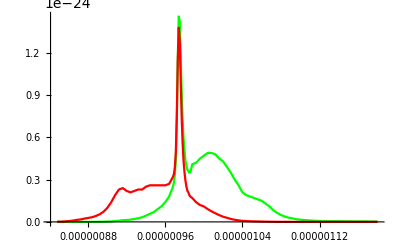

```mathematica
σlum=Transpose[{crossSections[[All, 1]]×10^-9, crossSections[[All,2]]}];
σabs=Transpose[{crossSections[[All, 1]]×10^-9, crossSections[[All,3]]}];
Show[ListLinePlot[σlum,PlotStyle->Green,PlotRange->All],ListLinePlot[σabs,PlotStyle->Red,PlotRange->All]]
```

```mathematica
σ12[λ_]:=Interpolation[σabs,λ];
σ21[λ_]:=Interpolation[σlum,λ];
```

```mathematica
σ12p=σ12[λp];
σ12s[λ_]:=σ12[λ];
σ21p=σ21[λp];
σ21s[λ_]:=σ21[λ];
```

```mathematica
Aeffs=(π×dcore^2)/4;
Aeffp=(π×dclad^2)/4×2;
```

#### Rate equations for fiber amplifier

```mathematica
ns[λ_,z_]:=(Ps[z,λi]×λ×nref)/(h×c^2×Aeffs);
np[z_]:=(Pp[z]×λp×nref)/(h×c^2×Aeffp);
N1N2=Solve[{0==v×np[z]×(σ12p×N1[z]-σ21p×N2[z])+Sum[v×ns[λi,z]×(σ12s[λi]×N1[z]-σ21s[λi]×N2[z]),{λi,λsmin,λsmax,(λsmax-λsmin)/λn}]-N2[z]/τ,N1[z]+N2[z]==Nions},{N1[z],N2[z]}];
N1[z_]=Evaluate[N1[z]/.N1N2][[1]];
N2[z_]=Evaluate[N2[z]/.N1N2][[1]];
```

```mathematica
eqns = Table[{D[Ps[z,λi],z]== 
   Ps[z,λi]×(σ21s[λi]×N2[z]-σ12s[λi]×N1[z]), Ps[0,λi] == Ps0/λn}, {λi,λsmin,λsmax,(λsmax-λsmin)/λn}];
vars = Table[Ps[z,λi],  {λi,λsmin,λsmax,(λsmax-λsmin)/λn}];
AppendTo[eqns,{D[Pp[z],z]==Pp[z]×(σ21p×N2[z]-σ12p×N1[z])×(Aeffs/Aeffp),Pp[0]==Pp0}];
AppendTo[vars,Pp[z]];
sols1=NDSolve[eqns, vars, {z,0,L}];
```

Pump and total signal power along the fiber amplifier (red and green respectively)

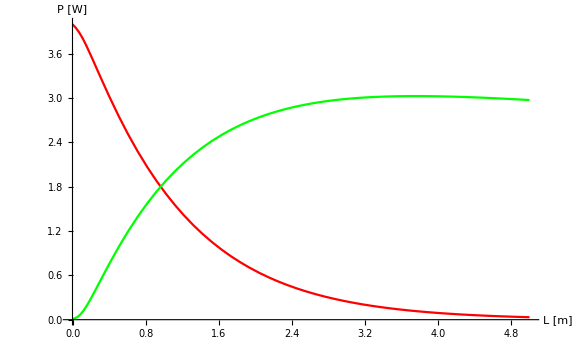

```mathematica
Show[Plot[Pp[z]/.sols1,{z,0,L},PlotStyle->Red,PlotRange->All,ImageSize->Large,AxesLabel->{"L [m]","P [W]"}],Plot[Sum[Ps[z,λi]/.sols1,{λi,λsmin,λsmax,(λsmax-λsmin)/λn}],{z,0,L},PlotStyle->Green,PlotRange->All,ImageSize->Large,AxesLabel->{"L [m]","P [W]"}]]
```

Signal power distribution at different wavelengths

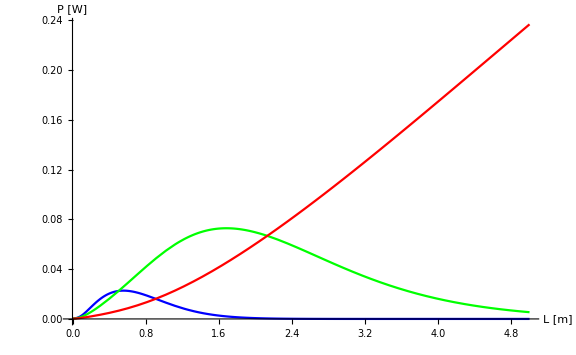

```mathematica
Show[Plot[Ps[z,λsmin]/.sols1,{z,0,L},PlotStyle->Blue,PlotRange->All,ImageSize->Large,AxesLabel->{"L [m]","P [W]"}],Plot[Ps[z,(λsmin+λsmax)/2]/.sols1,{z,0,L},PlotStyle->Green,PlotRange->All,ImageSize->Large,AxesLabel->{"L [m]","P [W]"}],Plot[Ps[z,λsmax]/.sols1,{z,0,L},PlotStyle->Red,PlotRange->All,ImageSize->Large,AxesLabel->{"L [m]","P [W]"}]]
```

Inversion distribution

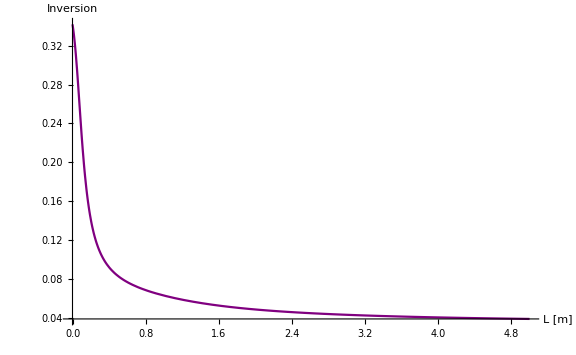

```mathematica
Plot[(N2[z]/.sols1)/Nions,{z,0,L},PlotStyle->Purple,PlotRange->All,ImageSize->Large,AxesLabel->{"L [m]","Inversion"}]
```

Spectrum after the amplifier

```mathematica
outSpectrum=Table[0,{i,λn},{j,2}];
For[i=1,i≤λn,i++,Subscript[funcPs,i][z_]=Ps[z,λsmin+(λsmax-λsmin)/λn×(i-1)]/.sols1;outSpectrum[[i,2]]=FullSimplify[Subscript[funcPs,i][L]];outSpectrum[[i,1]]=λsmin+(λsmax-λsmin)/λn×(i-1)];
outSpectrum=Partition[Flatten[outSpectrum],2];
```

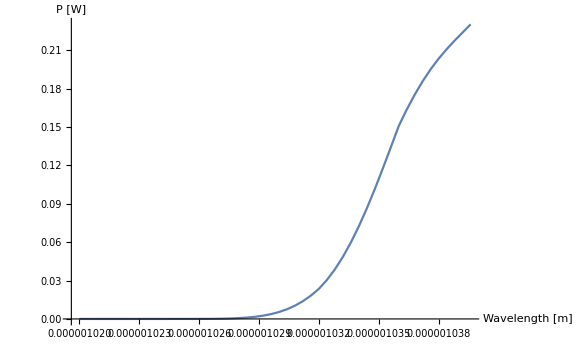

```mathematica
ListLinePlot[outSpectrum,ImageSize->Large,AxesLabel->{"Wavelength [m]","P [W]"}]
```

If we want the signal spectrum to be relatively unchanged, we can decrease amplifier length to 20 cm